# CForms for Simulink implementation

Table of Contents 
1. Definition of System Model
2. Partial Linearization and Design of Lower-level Controller

## 1. Model Equations

### Electricity

```mathematica
dδdt[δ_,ω_,i_,j_]:=1/Subscript[te, i] Subscript[ω, i]
dωdt[δ_,ω_,i_,j_]:=1/Subscript[te, i](Subscript[Pm, i] -Subscript[Da, i] Subscript[ω, i] -Subscript[Ee, i]^2 Subscript[G, i,i]-Subscript[Ee, i] Subscript[Ee, 0](Subscript[B, i,0] Sin[Subscript[δ, i]]+Subscript[G, i,0] Cos[Subscript[δ, i]]) -Subscript[Ee, i] Subscript[Ee, j](Subscript[B, i,j] Sin[Subscript[δ, i]-Subscript[δ, j]] -Subscript[G, i,j] Cos[Subscript[δ, i]-Subscript[δ, j]])) 
Subscript[P, inf][δ1_,ω1_,δ2_,ω2_]:=(-Subscript[G, 0,0] Subscript[Ee, 0]^2+Subscript[Ee, 1] Subscript[Ee, 0](Subscript[B, 1,0] Sin[δ1]-Subscript[G, 1,0] Cos[δ1])+Subscript[Ee, 2] Subscript[Ee, 0](Subscript[B, 2,0] Sin[δ2]-Subscript[G, 2,0] Cos[0-δ2]));
```

### Heat

```mathematica
dp1dt[p1_,p2_,U_]:=1/Subscript[th, 1](Q1- Subscript[QL, 1] -π/4 Subscript[h, c] Subscript[ρ, s] U)
dp2dt[p1_,p2_,U_]:=1/Subscript[th, 2](Q2- Subscript[QL, 2] +π/4 Subscript[h, c] Subscript[ρ, s] U)
dwdt[p1_,p2_,U_]:=1/Subscript[th, 3]((p1-p2)/Subscript[ρ, s]-(λ L)/(2d)U U )
Subscript[Q, 12][p1_,p2_,U_]:= π/4 Subscript[h, c] Subscript[ρ, s] U ;
Subscript[p, mean][p1_,p2_,U_]:= (p1+p2)/2 ;
```

### Gas turbine

```mathematica
Subscript[fg, 1][u_,V_,Pg_,Pgg_,i_]:= 1/Subscript[tv, i] (-Subscript[V, i]+(1-Subscript[α, i])Subscript[u, i]+Subscript[α, i]) 
Subscript[fg, 2][u_,V_,Pg_,Pgg_,i_]:=1/Subscript[tf, i](Subscript[V, i] - Subscript[Pg, i])
Subscript[fg, 3][u_,V_,Pg_,Pgg_,i_]:=1/Subscript[tcd, i](Subscript[Pg, i] - Subscript[Pgg, i])
pm[Pgg_,α_,i_]:=Subscript[ke, i] 1/(1-Subscript[α, i])( Subscript[Pgg, i]-Subscript[α, i])
q[Pg_,i_]:=Subscript[kh, i] 1/(1+Subscript[β, i])(Subscript[Pg, i]+Subscript[β, i])
```

### Setting of parameters

```mathematica
ratedvalues = {Subscript[Q, r]-> 1000*10^3,Subscript[h, r]->(800*10^3)/4.16,Subscript[ρ, r]-> 4.16,Subscript[e, 1]->3800,Subscript[e, 2]->3800,L->200,d->0.2};
parameter=Flatten[Join[Table[
{Subscript[tv, i]->0.05,Subscript[tf, i]->0.4,Subscript[tcd, i]->0.1,Subscript[α, i]->0.23,Subscript[β, i]->0},{i,2}],
{Subscript[ke, 1]->1.5,Subscript[ke, 2]->0.6,Subscript[kh, 1]->6,Subscript[kh, 2]->6},
{ Subscript[te, 1]-> 0.23,Subscript[te, 2]->0.23,Subscript[Da, 1]->0.05,Subscript[Da, 2]->0.05,Subscript[Ee, 0]->1,Subscript[Ee, 1]->1,Subscript[Ee, 2]->1},{Subscript[B, 1,0]->1,Subscript[B, 2,0]->1,Subscript[B, 1,2]->0.5,Subscript[B, 2,1]->0.5,Subscript[G, 0,0]->0,Subscript[G, 1,1]->0.0,Subscript[G, 2,2]->0,Subscript[G, 1,0]->0,Subscript[G, 2,0]->0,Subscript[G, 1,2]->0,Subscript[G, 2,1]->0},
{Subscript[QL, 1]->2,Subscript[QL, 2]->5,λ->0.016,L->200,d->0.2},
{Subscript[th, 1]->(Subscript[Q, r] Subscript[e, 1])/(d^4 Subscript[h, r]^2 Subscript[ρ, r]),Subscript[th, 2]->(Subscript[Q, r] Subscript[e, 1])/(d^4 Subscript[h, r]^2 Subscript[ρ, r]),Subscript[th, 3]->(d^2 L Subscript[ρ, r] Subscript[h, r])/Subscript[Q, r],Subscript[h, c]->(2047*10^3)/Subscript[h, r],Subscript[ρ, s]-> 4.16/Subscript[ρ, r]}/. ratedvalues
]]
Subscript[w, rated]= Subscript[Q, r]/(d^2*Subscript[h, r]*Subscript[ρ, r])/.ratedvalues;
Subscript[p, rated]= Subscript[ρ, r]*Subscript[w, rated]^2 /. ratedvalues;
```

{tv_1→0.05,tf_1→0.4,tcd_1→0.1,α_1→0.23,β_1→0,tv_2→0.05,tf_2→0.4,tcd_2→0.1,α_2→0.23,β_2→0,ke_1→1.5,ke_2→0.6,kh_1→6,kh_2→6,te_1→0.23,te_2→0.23,Da_1→0.05,Da_2→0.05,Ee_0→1,Ee_1→1,Ee_2→1,B_(1,0)→1,B_(2,0)→1,B_(1,2)→0.5,B_(2,1)→0.5,G_(0,0)→0,G_(1,1)→0.,G_(2,2)→0,G_(1,0)→0,G_(2,0)→0,G_(1,2)→0,G_(2,1)→0,QL_1→2,QL_2→5,λ→0.016,L→200,d→0.2,th_1→15.4375,th_2→15.4375,th_3→6.4,h_c→10.6444,ρ_s→1.}

### Vector fields for model implementation

```mathematica
DerivOfElectricity = { dδdt[δ,ω,1,2],dωdt[δ,ω,1,2], dδdt[δ,ω,2,1],dωdt[δ,ω,2,1] }  /. parameter /. {Subscript[δ, 1]-> del1, Subscript[δ, 2]-> del2, Subscript[ω, 1]-> omg1,  Subscript[ω, 2]-> omg2, Subscript[Pm, 1]-> pm1, Subscript[Pm, 2]-> pm2}
```

{4.34783 omg1,4.34783 (0.-0.05 omg1+pm1-Sin[del1]-0.5 Sin[del1-del2]),4.34783 omg2,4.34783 (-0.05 omg2+pm2+0.5 Sin[del1-del2]-Sin[del2])}

```mathematica
DerivOfHeat = { dp1dt[p1,p2,w],dp2dt[p1,p2,w],dwdt[p1,p2,w] }  /. parameter
```

{0.0647773 (-2+Q1-8.36009 w),0.0647773 (-5+Q2+8.36009 w),0.15625 (1. (p1-p2)-8. w^2)}

```mathematica
DerivOfGasTurbine = 
Join[Table[Subscript[fg, i][u,V,Pg,Pgg,1],{i,3} ] (* gas turbine *),Table[Subscript[fg, i][u,V,Pg,Pgg,2],{i,3} ] ] /.parameter /. {Subscript[u, 1]->u1,Subscript[u, 2]->u2, Subscript[V, 1]->x1,Subscript[Pg, 1]->x2,Subscript[Pgg, 1]->x3,Subscript[V, 2]->x4,Subscript[Pg, 2]->x5,Subscript[Pgg, 2]->x6}
```

{20. (0.23+0.77 u1-x1),2.5 (x1-x2),10. (x2-x3),20. (0.23+0.77 u2-x4),2.5 (x4-x5),10. (x5-x6)}

```mathematica
OutputOfGasTurbine = { pm[Pgg,α,1],  pm[Pgg,α,2], q[Pg,1], q[Pg,2]} /.parameter /. {Subscript[u, 1]->u1,Subscript[u, 2]->u2, Subscript[V, 1]->x1,Subscript[Pg, 1]->x2,Subscript[Pgg, 1]->x3,Subscript[V, 2]->x4,Subscript[Pg, 2]->x5,Subscript[Pgg, 2]->x6}
```

{1.94805 (-0.23+x3),0.779221 (-0.23+x6),6 x2,6 x5}

### State Space Model

```mathematica
Subscript[fe, 1][δ_,ω_,i_,j_] = dδdt[δ,ω,i,j];
Subscript[fe, 2][δ_,ω_,i_,j_] = dωdt[δ,ω,i,j] /.{Subscript[Pm, i]-> pm[Pgg,α,i]};
Subscript[fh, 1][p1_,p2_,U_] = dp1dt[p1,p2,U] /. {Q1 -> q[Pg,1]};
Subscript[fh, 2][p1_,p2_,U_]= dp2dt[p1,p2,U]/.{Q2->q[Pg,2]};
Subscript[fh, 3][p1_,p2_,U_]=dwdt[p1,p2,U] ;
```

```mathematica
n=13;
xt=Table[Subscript[x, i][t],{i,n}];
xfun={x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_,x11_,x12_,x13_}; (* 状態変数xについての関数を定義する時に使用 *)
xarg={x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13}; (* 定義した関数を呼び出すときに使用 *)
affine[xfun]=Join[
Table[Subscript[fg, i][u,V,Pg,Pgg,1],{i,3} ] (* gas turbine *),
Table[Subscript[fg, i][u,V,Pg,Pgg,2],{i,3} ] ,
Table[Subscript[fe, i][δ,ω,1,2],{i,2}] (*generator*),
Table[Subscript[fe, i][δ,ω,2,1],{i,2}],
Table[Subscript[fh, i][Subscript[p, 1],Subscript[p, 2],U],{i,3}](*heat system*)
] /. Join[{Subscript[V, 1]->x1,Subscript[Pg, 1]->x2,Subscript[Pgg, 1]->x3},{Subscript[V, 2]->x4,Subscript[Pg, 2]->x5,Subscript[Pgg, 2]->x6},{Subscript[δ, 1]->x7,Subscript[ω, 1]->x8,Subscript[δ, 2]->x9,Subscript[ω, 2]->x10}, {Subscript[p, 1]->x11,Subscript[p, 2]->x12,U->x13},{Subscript[u, 1]->u1,Subscript[u, 2]->u2}];
f[xfun]=affine[xarg]/.{u1->0,u2->0};
Subscript[g, 1][xfun]=Simplify[affine[xarg]-f[xarg]]/.{u1->1,u2->0};
Subscript[g, 2][xfun]=Simplify[affine[xarg]-f[xarg]]/.{u1->0,u2->1};
g[xfun]=Transpose[{Subscript[g, 1][xarg],Subscript[g, 2][xarg]}];
Subscript[h, 1][xfun]=Subscript[P, inf][x7,x8,x9,x10];
Subscript[h̄, 2][xfun]=Subscript[p, mean][x11,x12,x13];
Subscript[h, 2][xfun]=Subscript[Q, 12][x11,x12,x13];
h[xfun]={Subscript[h, 1][xarg],Subscript[h, 2][xarg]};
```

```mathematica
MatrixForm[f[xarg]]+MatrixForm[g[xarg]]
MatrixForm[h[xarg]];
```

((1-α_1)/tv_1 | 0
0 | 0
0 | 0
0 | (1-α_2)/tv_2
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0
0 | 0)+((-x1+α_1)/tv_1
(x1-x2)/tf_1
(x2-x3)/tcd_1
(-x4+α_2)/tv_2
(x4-x5)/tf_2
(x5-x6)/tcd_2
x8/te_1
(-x8 Da_1+(ke_1 (x3-α_1))/(1-α_1)-Ee_0 Ee_1 (Sin[x7] B_(1,0)+Cos[x7] G_(1,0))-Ee_1^2 G_(1,1)-Ee_1 Ee_2 (Sin[x7-x9] B_(1,2)-Cos[x7-x9] G_(1,2)))/te_1
x10/te_2
(-x10 Da_2+(ke_2 (x6-α_2))/(1-α_2)-Ee_0 Ee_2 (Sin[x9] B_(2,0)+Cos[x9] G_(2,0))-Ee_1 Ee_2 (-Sin[x7-x9] B_(2,1)-Cos[x7-x9] G_(2,1))-Ee_2^2 G_(2,2))/te_2
(-QL_1+(kh_1 (x2+β_1))/(1+β_1)-1/4 π x13 h_c ρ_s)/th_1
(-QL_2+(kh_2 (x5+β_2))/(1+β_2)+1/4 π x13 h_c ρ_s)/th_2
(-(L x13^2 λ)/(2 d)+(x11-x12)/ρ_s)/th_3)

```mathematica
TwoSiteSystem= (f[xarg] + g[xarg].{u1 ,u2}) /. parameter;
```

### Calculation of an equilibrium point

```mathematica
floweq=Join[f[Table[Subscript[x, i],{i,13}]]+g[Table[Subscript[x, i],{i,13}]].{Subscript[u, 1],Subscript[u, 2]},{Subscript[h, 1][Table[Subscript[x, i],{i,13}]]-Subscript[P, e,ref], Subscript[h̄, 2][Table[Subscript[x, i],{i,13}]]-Subscript[p, ref]}]/.parameter /.{Subscript[P, e,ref]-> 1.42,Subscript[p, ref]->0.00};
ep=FindRoot[floweq==0,
{{Subscript[x, 1],0.7},{Subscript[x, 2],0.7},{Subscript[x, 3],0.7},{Subscript[x, 4],0.7},{Subscript[x, 5],0.7},{Subscript[x, 6],0.7},{Subscript[x, 7],0.3},{Subscript[x, 8],0},{Subscript[x, 9],0.3},{Subscript[x, 10],0},{Subscript[x, 11],0},{Subscript[x, 12],0},{Subscript[x, 13],0}
,{Subscript[u, 1],0.7},{Subscript[u, 2],0.7}}]
equilibriumpoint = Table[Subscript[x, i],{i,13}]/. ep;
Φ[equilibriumpoint]/.parameter;  
Subscript[h, 2][Table[Subscript[x, i],{i,13}]]/.parameter/. ep
(* (ξ, η) at equilibrium point *)
```

{x_1→0.973778,x_2→0.973778,x_3→0.973778,x_4→0.192889,x_5→0.192889,x_6→0.192889,x_7→1.54955,x_8→0.,x_9→0.433694,x_10→0.,x_11→0.845091,x_12→-0.845091,x_13→0.459644,u_1→0.965945,u_2→-0.0481962}

3.84267

{0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4}

{-0.88,-0.366667,0.146667,0.66,1.17333,1.68667,2.2,2.71333,3.22667,3.74}

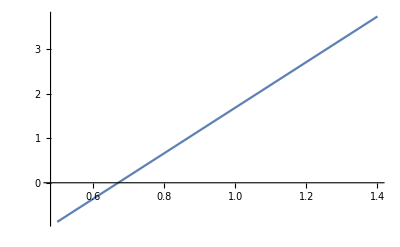

```mathematica
floweq=Join[f[Table[Subscript[x, i],{i,13}]]+g[Table[Subscript[x, i],{i,13}]].{Subscript[u, 1],Subscript[u, 2]},{Subscript[h, 1][Table[Subscript[x, i],{i,13}]]-Subscript[P, e,ref], Subscript[h̄, 2][Table[Subscript[x, i],{i,13}]]-Subscript[p, ref]}]/.parameter /.{Subscript[p, ref]->0.00};
PrefList = Range[0.5,1.4,0.1]
QrefList =Table[  Subscript[h, 2][Table[Subscript[x, i],{i,13}]]/.parameter/.FindRoot[floweq==0,{{Subscript[x, 1],0.7},{Subscript[x, 2],0.7},{Subscript[x, 3],0.7},{Subscript[x, 4],0.7},{Subscript[x, 5],0.7},{Subscript[x, 6],0.7},{Subscript[x, 7],0.3},{Subscript[x, 8],0},{Subscript[x, 9],0.3},{Subscript[x, 10],0},{Subscript[x, 11],0},{Subscript[x, 12],0},{Subscript[x, 13],0}
,{Subscript[u, 1],0.7},{Subscript[u, 2],0.7}}], {Subscript[P, e,ref],0.5,1.45,0.1}]
ListLinePlot[Transpose[{PrefList,QrefList}]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["./simex2_equilibriums.csv",Transpose[{PrefList,QrefList}]]
```

C:\Users\hoshino\Documents\01_UHyogo\01Research\paper\202207chp\simulation

./simex2_equilibriums.csv

### Calculation of steady flow

```mathematica
equilXe = f[xarg][[{8,10}]]/.{x7->del1,x8 -> 0,x9->del2,x10->0, x3->(1-Subscript[α, 1])u1+Subscript[α, 1], x6->(1-Subscript[α, 2])u2+Subscript[α, 2]} /. parameter ;
equilElec =FindRoot[equilXe ==0/. {u1-> 0.5, u2 -> 0.5}, {{del1,0.3},{del2,0.3}}]
flowElec = Subscript[h, 1][xarg] /.{x7->del1,x9->del2} /.parameter
flowElec /.equilElec
```

{del1→0.679893,del2→0.434868}

Sin[del1]+Sin[del2]

1.05

```mathematica
equilXh = {f[xarg][[11]]- f[xarg][[12]],  f[xarg][[13]] }  \
/. { x2->(1-Subscript[α, 1])u1+Subscript[α, 1], x5->(1-Subscript[α, 2])u2+Subscript[α, 2], x11-x12->delP, x13->w}/.parameter
equilHeat = FindRoot[equilXh == 0 /. {u1-> 0.5, u2 -> 0.5}, {{w,0}, {delP,0}}];
flowHeat = Subscript[h, 2][xarg] /. {x13->w} /.parameter;
flowHeat /.equilHeat
```

{0.0647773 (-2+6 (0.23+0.77 u1)-8.36009 w)-0.0647773 (-5+6 (0.23+0.77 u2)+8.36009 w),0.15625 (1. delP-8. w^2)}

1.5

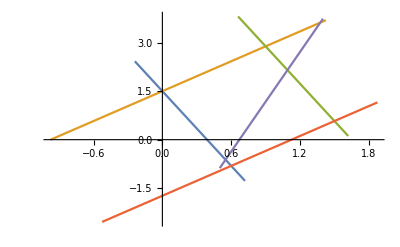

```mathematica
umin = 0.0;
umax = 0.6;
u2max = 1.0;
data1m = Table[ {flowElec /. FindRoot[equilXe ==0/. {u1->umin, u2 -> uspan}, {{del1,0.3},{del2,0.3}}],                    flowHeat /. FindRoot[equilXh == 0 /.{u1-> umin, u2 -> uspan}, {{w,0}, {delP,0}}] },{uspan,-0.4,1.2,0.05}];
data2m = Table[ {flowElec /. FindRoot[equilXe ==0/. {u1->uspan, u2 -> umin}, {{del1,0.3},{del2,0.3}}],                        flowHeat /. FindRoot[equilXh == 0 /. {u1-> uspan, u2 -> umin}, {{w,0}, {delP,0}}]}, {uspan,-0.65,0.95,0.05}];
data1M = Table[ {flowElec /. FindRoot[equilXe ==0/. {u1->umax, u2 -> uspan}, {{del1,0.3},{del2,0.3}}],                        flowHeat/. FindRoot[equilXh == 0 /. {u1-> umax, u2 -> uspan}, {{w,0}, {delP,0}}]}, {uspan,-0.4,1.2,0.05}];
data2M = Table[ {flowElec /. FindRoot[equilXe ==0/. {u1->uspan, u2 -> u2max}, {{del1,0.3},{del2,0.3}}],                       flowHeat/. FindRoot[equilXh == 0 /. {u1-> uspan, u2 -> u2max}, {{w,0}, {delP,0}}]}, {uspan,-0.75,0.85,0.05}];
ListLinePlot[{data1m,data2m,data1M,data2M,Transpose[{PrefList,QrefList}]}]
```

```mathematica
data = Transpose[Join[Transpose[data1m],Transpose[data2m],Transpose[data1M], Transpose[data2M]]];
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["./simex2_constrains.csv",data]
```

C:\Users\hoshino\Documents\01_UHyogo\01Research\paper\202207chp\simulation

./simex2_constrains.csv